# UniDyn--Demo-04.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  Use the UniDyn Evolver function to calculate the evolution of the magnetization of a two coupled spin = 1/2 particles.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$UniDynPath ="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
```

/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn/UniDyn.m

Now that we are confident that the path is set correctly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True;
Needs["UniDyn`"]
```

CreateOperator::usage: CreateOperator[] is used to batch-define a bunch of operators.   Example: CreateOperator[{{Ix, Iy, Iz},{Sx,Sy,Sz}}] will create six operators, where each of the operators in the first list will commute with each of the operators of the second list.

CreateScalar::usage: CreateScalar[list] is used to batch-define a bunch of scalars.  The parameter list can be a single scalar or a list of scalars.  Example: CreateScalar[{w1,w2}].

NCSort::usage: NCSort[list] sorts the operators in list into canonical order.

SortedMult::usage: SortedMult[list] returns Mult[list$ordered], where list$ordered are the elements of list sorted into canonical order.

MultSort::usage: MultSort[NonCommutativeMultiplyt[list]] returns returns NonCommutativeMultiply[list$ordered], where list$ordered are the elements of list sorted into canonical order.

Comm::usage: Comm[a,b] calculates the commutator of two operators.

SpinSingle$CreateOperators::usage: SpinSingle$CreateOperators[Ix,Iy,Iz,L] creates Ix, Iy, and Iz angular momentum operators and defines their commutation relations.  When the total angular momentum L = 1/2, additional rules are defined to simplify products of the angular momentum operators.  When the total angular momentum L is unspecified, no such simplification rules are defined.

OscSingle$CreateOperators::usage: OscSingle$CreateOperators[aL,aR] creates a raising operator aR and a lowering operator aL for single harmonic oscillator and defines the operator commutation relations.

Evolve::usage: Evolve[H, t, ρ] represents unitary evolution of the density operator ρ for a time t under the Hamiltonian H.  This function expands according to simplification rules but leaves the evolution unevaluated.

Evolver::usage: Evolver[H, t, ρ(0)] calculates ρ(t) = Exp[-I H t] ρ(0) Exp[+I H t], assuming that H is time independent, according to the commutation rules followed by ρ(0) and H.

## Evolver with simplification

```mathematica
SimplifyingEvolver[H_,t_,ρ$0_]:=  
	Evolver[H, t, ρ$0]//Simplify// ExpToTrig // FullSimplify
```

## Unitary evolution of a single spin 1/2

### Create a single spin

The assumptions define below are required for Mathematica to recognize √(–Δ^2-ω^2)= I √(Δ^2+ω^2) inside an exponential.   One of the variables has to be defined to be > 0 and not just ⩾ 0.

```mathematica
Clear[
Δω,                     (* resonance offset frequency *)
ω$1,                  (* Rabi frequency of the applied irradiation *)
t,                      (* time *)
Ix, Iy, Iz,  (* spin angular momentum operators *)
ρ$0,                  (* initial spin density operator *)
H                          (* spin Hamiltonian *)]

CreateScalar[Δω,ω$1, t];
SpinSingle$CreateOperators[Ix, Iy, Iz, L=1/2];

$Assumptions  = {Element[Δω, Reals], Δω ⩾ 0, Element[ω$1, Reals], ω $1 > 0, Element[t, Reals], t ⩾ 0};
```

SpinSingle$CreateOperators::create: Creating spin operators.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

### On-resonance nutation

On-resonance irradiation Hamiltonian written in the interaction representation.  The initial density operator is parallel to I_x.

```mathematica
H = ω$1 Ix;
ρ$0 = Iz;
```

Calculate the time-dependent density operator.

```mathematica
SimplifyingEvolver[H,t,ρ$0] /. { ω$1-> Subscript[ω,1]}
```

Iz Cos[t ω_1]-Iy Sin[t ω_1]

### Free evolution

Zeeman-interaction Hamiltonian written in the interaction representation.  The initial density operator is parallel to I_x.

```mathematica
H = Δω Iz;
ρ$0 = Ix;
```

Calculate the time-dependent density operator.

```mathematica
SimplifyingEvolver[H,t,ρ$0]
```

Ix Cos[t Δω]+Iy Sin[t Δω]

## Unitary evolution of two coupled spins

### Create a two spins

The assumptions define below are required for Mathematica to recognize √(–Δ^2-ω^2)= I √(Δ^2+ω^2) inside an exponential.   One of the variables has to be defined to be > 0 and not just ⩾ 0.

```mathematica
Clear[

Δ$I,                 (* resonance offset frequency *)
Δ$S,                 (* resonance offset frequency *)
J,                      (* spin-spin coupling *)
Ix, Iy, Iz, (* spin angular momentum operators *)
Sx, Sy, Sz, (* spin angular momentum operators *)
ρ,                      (* spin density operator *) 
t,                       (* time *)
ρ$0,                  (* initial spin density operator *)
H                          (* spin Hamiltonian *)]

CreateScalar[Δ$I,Δ$S,J,t ];
CreateOperator[{{Ix, Iy, Iz},{Sx, Sy, Sz}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, L=1/2];
SpinSingle$CreateOperators[Sx, Sy, Sz, L=1/2];

$Assumptions  = {Element[Δ$I, Reals], Δ$I ⩾ 0, Element[Δ$S, Reals], Δ$S ⩾ 0, Element[J, Reals], J  > 0};
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

### Evolution under J coupling

On-resonance irradiation Hamiltonian written in the interaction representation.  The initial density operator is parallel to I_x.

```mathematica
H$0 = Δ$I Iz + Δ$S Sz;
H$J =  J Mult[Iz,Sz];
ρ$0 = Ix;
```

Try to calculate the density operator in a single step.

```mathematica
SimplifyingEvolver[H$0+H$J,t, ρ$0]
```

Evolver::unsolvable: Unrecognized evolution

{Ix,Iy Δ$I+J Mult[Iy,Sz],-1/4 Ix (J^2+4 Δ$I^2)-2 J Δ$I Mult[Ix,Sz],-1/4 Iy Δ$I (3 J^2+4 Δ$I^2)-1/4 (J^3+12 J Δ$I^2) Mult[Iy,Sz],1/16 Ix (J^4+24 J^2 Δ$I^2+16 Δ$I^4)+J Δ$I (J^2+4 Δ$I^2) Mult[Ix,Sz]}

This single-step evolution fails.  Instead, let us calculate the density operator in two steps.  We can do this because the H$J and H$0 Hamiltonians commute. Evolve under the J-coupling first and under the chemical shift second.

```mathematica
ρ = ρ$0// SimplifyingEvolver[H$J,t, #]& // SimplifyingEvolver[H$0,t, #]&
```

Cos[(J t)/2] (Ix Cos[t Δ$I]+Iy Sin[t Δ$I])+2 Sin[(J t)/2] (Cos[t Δ$I] Mult[Iy,Sz]-Mult[Ix,Sz] Sin[t Δ$I])

Try another way -- evolve under the chemical shift first and under the J-coupling second.

```mathematica
ρ = ρ$0// SimplifyingEvolver[H$0,t, #]& // SimplifyingEvolver[H$J,t, #]&
```

Cos[(J t)/2] (Ix Cos[t Δ$I]+Iy Sin[t Δ$I])+2 Sin[(J t)/2] (Cos[t Δ$I] Mult[Iy,Sz]-Mult[Ix,Sz] Sin[t Δ$I])

We see by inspection that we get the same answer either way.

### Load spin 1/2 operator matrices

Load matrices representing two J=1/2 spins and give them a test drive.

```mathematica
<<Matrices--two-spin-half.m
```

Loaded spin one-half matrices for mIx, mIy, mIz, mSx, mSy, mSz

Let's look at one of the matrices, the matrix for Iz.

```mathematica
mIz // MatrixForm
mSz // MatrixForm
```

(-1/2 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | 1/2)

(-1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | 1/2)

For a single spin 1/2 particle, Iz is a 2 x 2 matrix.  In the product space of two spin 1/2 particles, however, the Iz is now a 4 x 4 matrix.  All the operators are 4 x 4 matrices.

Check that the [Ix, Iy]/I = Iz and [Sx, Sy]/I = Sz commutation relations hold with the matrices.

```mathematica
m$1= (mIx . mIy - mIy.mIx)/I ; 
m$2 = (mSx . mSy - mSy.mSx)/I ;
```

```mathematica
m$1 // MatrixForm (* should be Iz *)
m$2 // MatrixForm (* should be Sz *)
```

(-1/2 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | 1/2 | 0
0 | 0 | 0 | 1/2)

(-1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | 1/2)

Make the (matrix) operator I$total = Iz + Sz.  We can see by inspection that this matrix looks correct.  The I$total operator should have eigenvalues {-1,0,0,+1}.  The matrix I$total is diagonal and we can read the eigenvalues off diagonal elements.

```mathematica
m$1 + m$2 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

### Calculate the analytical signal using the matrices

Write the matrix representation of Iy Sz using the matrices loaded above.

```mathematica
mIy . mSz // MatrixForm
```

(0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/4
ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/4 | 0 | 0)

Show that we can obtain the same matrix from the symbolic product Iy**Sz by (1) substituting the spin operators with matrices and (2) replacing the NonCommutativeMultiply operator with the Dot (i.e., matrix multiplication) operator.

```mathematica
Mult[Iy,Sz] //. Mult -> Dot /. {Ix-> mIx, Iy-> mIy, Iz-> mIz, Sx-> mSx, Sy-> mSy, Sz-> mSz}  // MatrixForm
```

(0 | 0 | -ⅈ/4 | 0
0 | 0 | 0 | ⅈ/4
ⅈ/4 | 0 | 0 | 0
0 | -ⅈ/4 | 0 | 0)

```mathematica
ρ // Expand
```

Ix Cos[(J t)/2] Cos[t Δ$I]+2 Cos[t Δ$I] Mult[Iy,Sz] Sin[(J t)/2]+Iy Cos[(J t)/2] Sin[t Δ$I]-2 Mult[Ix,Sz] Sin[(J t)/2] Sin[t Δ$I]

Calculate the density operator matrix.

```mathematica
Clear[ρ$matrix,ρ$temp, t];
ρ$temp = Expand[ρ] /. Mult -> Dot;
ρ$matrix[t_]  = ρ$temp /. {Ix-> mIx, Iy-> mIy, Iz-> mIz, Sx-> mSx, Sy-> mSy, Sz-> mSz};
```

Check that the resulting object is a 4 x 4 matrix as expected.

```mathematica
Dimensions[ρ$matrix[t]]
```

{4,4}

From this matrix we can calculate the I-spin signals as Trace[ρ Ix] and Trace[ρ Iy]

```mathematica
Tr[ρ$matrix[t] . mIx] // Simplify
Tr[ρ$matrix[t] . mIy] // Simplify
```

Cos[(J t)/2] Cos[t Δ$I]

Cos[(J t)/2] Sin[t Δ$I]

We can mimic the complex signal collected by the NMR spectrometer by calculating the expectation value of the Ix + I Iy operator: Trace[ρ (Ix+ I Iy)].

```mathematica
Clear[S];
S[t_]:= Tr[ρ$matrix[t] . (mIx- I mIy)]  // TrigToExp
```

### Plot the signal as a function of time

Create a more realistic experimental signal by multiplying the above-calculated signal by a decaying exponential.

```mathematica
Clear[S$expt];
S$expt[t_] := S[t] Exp[-t/T2]
```

To plot, set the total number of points (NN) and the total time (T).  We set NN equal to a power of 2 in anticipation of taking a digital Fourier transform.

```mathematica
NN = 2^10;
T$final = 10.0;
```

From NN and T$final we derive the time step (dt) and the frequency step (df).  Now generate a list of data points based on the above function.  At the same time, generate a list of time points (t) and frequency points (f) for plotting.

```mathematica
dt = T$final/(NN-1);
df = 1/dt;

f$table = Table[jj/T$final,{jj,-NN/2,NN/2-1}];
t$table = Table[ii*dt,{ii,0,NN-1}];

Print["The time step is ",dt," s"]
Print["The Nyquist frequency is ",1/(2*dt)," Hz"]
```

The time step is 0.00977517 s

The Nyquist frequency is 51.15 Hz

Give numbers for the chemical shift and the J-coupling.

```mathematica
Δ$I$value = 2π ×10.0;    (* chemical shift [rad/s] *)
J$value =  2π × 8.0;         (* heteronuclear scalar coupling constant [rad/s] *)
T2$value = 1.0;                  (* spin dephasing time [s] *)
```

Create an array of complex signal.

```mathematica
S$table = S$expt[t] /. {t-> t$table, Δ$I -> Δ$I$value, J-> J$value, T2 -> T2$value};
```

Plot the real and imaginary part of the signal

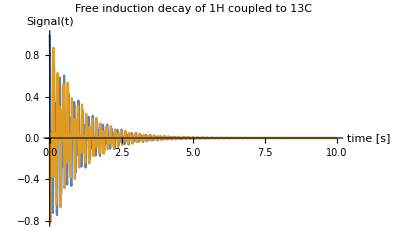

```mathematica
ListLinePlot[
{
{t$table, Re[S$table]} // Transpose,
{t$table, Im[S$table]} // Transpose},
Joined->True,
PlotRange->All,
PlotLabel->"Free induction decay of 1H coupled to 13C\n",
AxesLabel->{"time [s]","Signal(t)"}]
```

A function to calculate the digital Fourier transform of signal.

```mathematica
DFFT[signal$table_,time$table_, query_:True] := (* True to plot both real and imaginary FT parts *)
Module[{NN,T$final},

NN = Dimensions[signal$table][[1]];
FFTS$table= RotateRight[Fourier[signal$table],NN/2];

T$final = time$table[[-1]];
f$table= Table[jj/T$final,{jj,-NN/2,NN/2-1}];

p1= ListLinePlot[
{Transpose[{time$table,Re[signal$table]}],
Transpose[{time$table,Im[signal$table]}]},
PlotRange->{-1,1},
AxesLabel-> {"time [s]","signal"}];

If[query == True,

p2=ListLinePlot[
{Transpose[{f$table,Re[FFTS$table]}],
Transpose[{f$table,Im[FFTS$table]}] },
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}],

p2=ListLinePlot[
Transpose[{f$table,Re[FFTS$table]}],
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}]
];

Show[GraphicsGrid[{{p1,p2}}]]
]
```

Fourier transform the signal to obtain the spectrum.

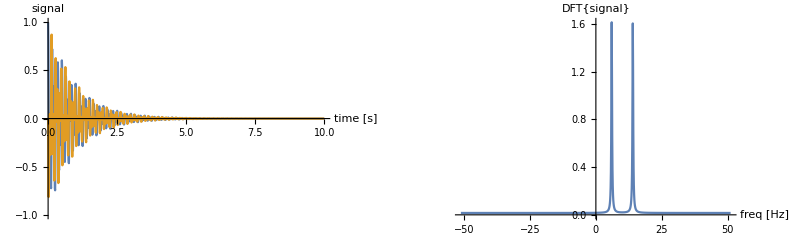

```mathematica
DFFT[S$table,t$table, False]
```

Find peaks in the FT spectrum.  Require the peaks to be larger than 1.0.   See the FindPeaks function documentation here.

```mathematica
peaks = FindPeaks[Re[FFTS$table], 0, 0, 1.]
```

{{573,1.61249},{653,1.60297}}

Read out the frequencies at which the peaks are located.  We see peaks at the expected frequencies of 10-8/2 = 6 Hz and 10+8/2 = 14 Hz.

```mathematica
Part[f$table,Transpose[peaks][[1]]]
```

{6.,14.}

## Clean up